```mathematica
32*32*2
```

2048

```mathematica
Statistical = Import["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data\\Volume_2048_statistical.csv"];
sorted = SortBy[Statistical,-#[[2]]&];
actions = sorted[[;;,2]];
```

```mathematica
Mean[Table[N[StandardDeviation[ToExpression@ StringSplit[sorted[[i,1]],":"]]],{i,100}]]
Mean[Table[N[StandardDeviation[ToExpression@ StringSplit[sorted[[-i,1]],":"]]],{i,100}]]
```

43.5741

22.5642

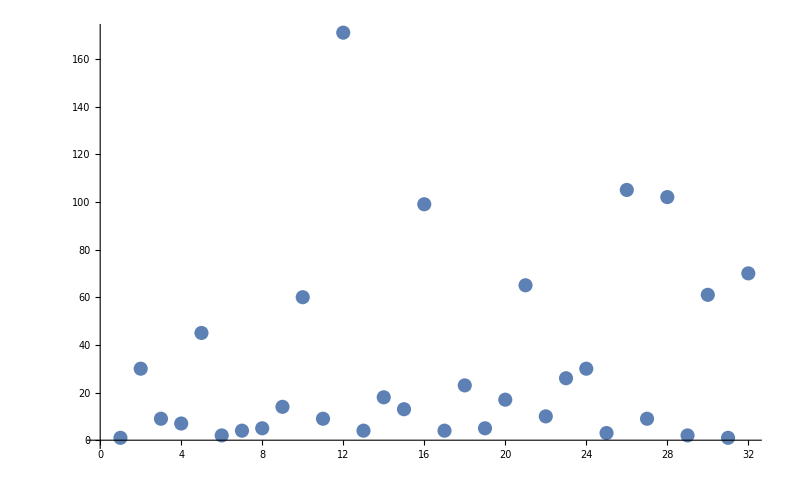

```mathematica
ListPlot[Table[N[ToExpression@ StringSplit[sorted[[i,1]],":"]],{i,100}][[2]]]
```

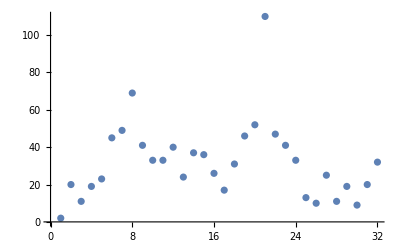

```mathematica
ListPlot[Table[N[ToExpression@ StringSplit[sorted[[-i,1]],":"]],{i,100}][[2]]]
```

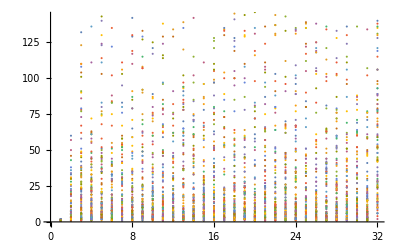

```mathematica
ListPlot[Table[N[ToExpression@ StringSplit[sorted[[i,1]],":"]],{i,100}]]
```

```mathematica
sorted[[1,2]]
sorted[[-1,2]]
```

6511.41

2054.85

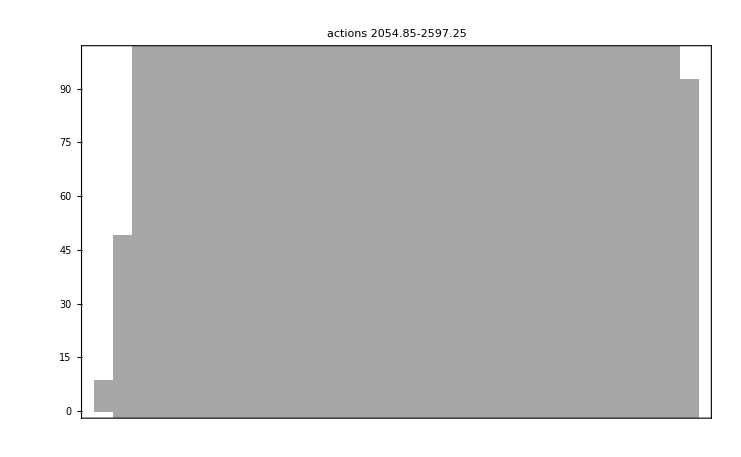

```mathematica
a = DistributionChart[Transpose[Table[N[ToExpression@ StringSplit[sorted[[-i,1]],":"]],{i,1000}]],PlotRange->{0,100},ChartElementFunction->ChartElementData["Density"],ChartStyle-> {Directive[EdgeForm[None],Orange]},BarSpacing->0,PlotLabel-> "actions "<>ToString[sorted[[-1,2]]]<>"-"<>ToString[sorted[[-1000,2]]]]
```

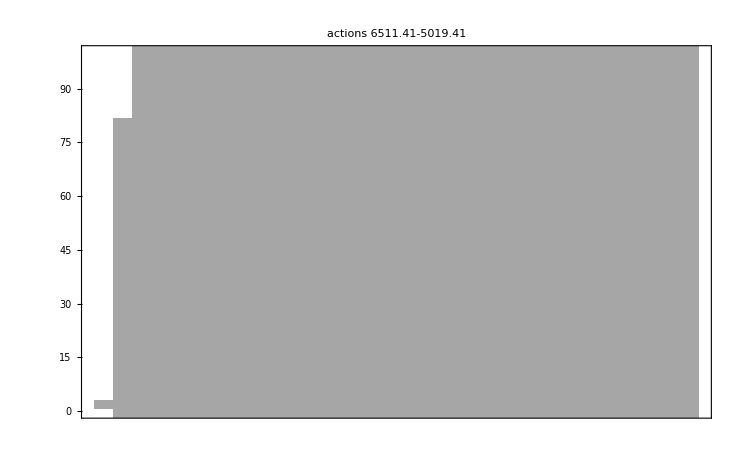

```mathematica
b = DistributionChart[Transpose[Table[N[ToExpression@ StringSplit[sorted[[i,1]],":"]],{i,1000}]],PlotRange->{0,100},ChartElementFunction->ChartElementData["Density"], ChartStyle-> {Directive[EdgeForm[None],Blue]},BarSpacing->0,PlotLabel-> "actions "<>ToString[sorted[[1,2]]]<>"-"<>ToString[sorted[[1000,2]]]]
```